```mathematica
sol=Solve[aa u^4+u+cc==0,u]
```

{{u→1/2 √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))-1/2 √(-(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))-((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)-2/(aa √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))))},{u→1/2 √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))+1/2 √(-(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))-((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)-2/(aa √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))))},{u→-1/2 √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))-1/2 √(-(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))-((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)+2/(aa √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))))},{u→-1/2 √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))+1/2 √(-(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))-((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)+2/(aa √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))))}}

```mathematica
CForm[sol[[3,1,2]]]
```

-Sqrt((4*Power(0.6666666666666666,0.3333333333333333)*cc)/
        Power(9*aa + Sqrt(3)*Sqrt(27*Power(aa,2) - 256*Power(aa,3)*Power(cc,3)),
         0.3333333333333333) + Power(9*aa + 
          Sqrt(3)*Sqrt(27*Power(aa,2) - 256*Power(aa,3)*Power(cc,3)),
         0.3333333333333333)/
        (Power(2,0.3333333333333333)*Power(3,0.6666666666666666)*aa))/2. - 
   Sqrt((-4*Power(0.6666666666666666,0.3333333333333333)*cc)/
       Power(9*aa + Sqrt(3)*Sqrt(27*Power(aa,2) - 256*Power(aa,3)*Power(cc,3)),
        0.3333333333333333) - Power(9*aa + 
         Sqrt(3)*Sqrt(27*Power(aa,2) - 256*Power(aa,3)*Power(cc,3)),
        0.3333333333333333)/
       (Power(2,0.3333333333333333)*Power(3,0.6666666666666666)*aa) + 
      2/(aa*Sqrt((4*Power(0.6666666666666666,0.3333333333333333)*cc)/
            Power(9*aa + Sqrt(3)*
               Sqrt(27*Power(aa,2) - 256*Power(aa,3)*Power(cc,3)),
             0.3333333333333333) + 
           Power(9*aa + Sqrt(3)*Sqrt(27*Power(aa,2) - 
                 256*Power(aa,3)*Power(cc,3)),0.3333333333333333)/
            (Power(2,0.3333333333333333)*Power(3,0.6666666666666666)*aa))))/2.

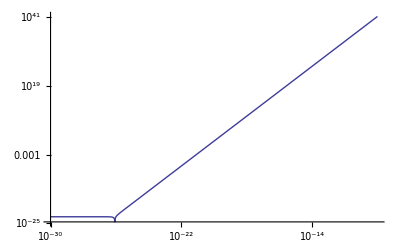

```mathematica
AA=2.14 10^81;
CC=-1.1258 10^-23;
LogLogPlot[Abs[AA u^4+u+CC],{u,10^-30,10^-10}]
```

```mathematica
sol[[1,1,2]]/.{aa->1.AA,cc->CC}
sol[[2,1,2]]/.{aa->1.AA,cc->CC}
sol[[3,1,2]]/.{aa->1.AA,cc->CC}
sol[[4,1,2]]/.{aa->1.AA,cc->CC}
```

1.61065×10^-30-8.51651×10^-27 ⅈ

1.61065×10^-30+8.51651×10^-27 ⅈ

-8.51812×10^-27

8.5149×10^-27

```mathematica
(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)/.{aa->1.AA,cc->CC}
```

1.03768×10^-59

```mathematica
(9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3)/.{aa->1.AA,cc->CC}
```

4.69711×10^29

```mathematica
(-(4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))-((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa)+2/(aa √((4 (2/3)^(1/3) cc)/((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))+((9 aa+√3 √(27 aa^2-256 aa^3 cc^3))^(1/3))/(2^(1/3) 3^(2/3) aa))))/.{aa->1.AA,cc->CC}
```

2.90124×10^-52